# Differential Matrices for Levin’s Method

## K Integrals

```mathematica
w={
SphericalBesselJ[l,α k]SphericalBesselJ[l,β k],
SphericalBesselJ[l+1,α k]SphericalBesselJ[l,β k],
SphericalBesselJ[l,α k]SphericalBesselJ[l+1,β k],
SphericalBesselJ[l+1,α k]SphericalBesselJ[l+1,β k]
};
```

```mathematica
dw=D[w,k]//FullSimplify;
```

```mathematica
dw//TraditionalForm
```

{2 lk α ((l lk α)/k-α l+1k α),α (lk α)^2-(2 l+1k α lk α)/k-α (l+1k α)^2,(2 l+1k α (α k lk α-(l+2) l+1k α))/k}

```mathematica
A={{2l/k,-α,-β,0},
{α,-2/k,0,-β},
{β,0,-2/k,-α},
{0, β,α,-2(l+2)/k}};
```

```mathematica
dw==A.w//FullSimplify
```

True

```mathematica
A//MatrixForm
```

((2 l)/k | -α | -β | 0
α | -2/k | 0 | -β
β | 0 | -2/k | -α
0 | β | α | -(2 (2+l))/k)

-8.35836559246804×10^-8

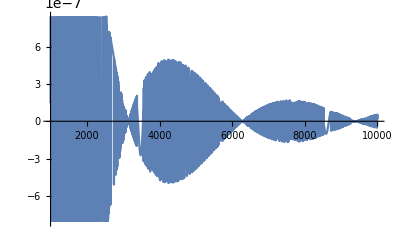

```mathematica
a=10^(3);
b=10^(4);
α=0.001;
β=100.0;
l=0;
ans=NIntegrate[SphericalBesselJ[l,α k]SphericalBesselJ[l,β k],{k,a,b},Method->"LevinRule"];
NumberForm[ans,16]
Plot[SphericalBesselJ[l,α k]SphericalBesselJ[l,β k],{k,a,b}]
```

## H Integrals

```mathematica
w={
SphericalBesselJ[l,α k]^2,
SphericalBesselJ[l+1,α k]SphericalBesselJ[l,α k],
SphericalBesselJ[l+1,α k]^2
};
```

```mathematica
dw=D[w,k]//FullSimplify;
```

```mathematica
dw //TraditionalForm
```

{2 lk α ((l lk α)/k-α l+1k α),α (lk α)^2-(2 l+1k α lk α)/k-α (l+1k α)^2,(2 l+1k α (α k lk α-(l+2) l+1k α))/k}

```mathematica
A = {{2l/k, -2α, 0},
{α, -2/k,-α},
{0,2α,-2(l+2)/k}};
```

```mathematica
A//MatrixForm
```

((2 l)/k | -2 α | 0
α | -2/k | -α
0 | 2 α | -(2 (2+l))/k)

```mathematica
dw==A.w//FullSimplify
```

```mathematica
True
a=1.0;
b=10.0;
α=0.01;
l=10;
ans=NIntegrate[k^6SphericalBesselJ[l,α k]^2,{k,a,b}];
NumberForm[ans,16]
```

True

1.958387322186554×10^-35

## I Integrals

```mathematica
w={
SphericalBesselJ[l,α k],
SphericalBesselJ[l+1,α k]
};
```

```mathematica
dw=D[w,k]//FullSimplify;
```

```mathematica
dw //TraditionalForm
```

{(l lk α)/k-α l+1k α,α lk α-((l+2) l+1k α)/k}

```mathematica
A={{l/k,-α},
{α,-(l+2)/k}};
```

```mathematica
A//MatrixForm
```

(l/k | -α
α | (-2-l)/k)

```mathematica
dw==A.w//FullSimplify
```

True

```mathematica
a=1.0;
b=10.0;
α=0.01;
l=10;
ans=NIntegrate[k^6SphericalBesselJ[l,α k],{k,a,b}];
NumberForm[ans,16]
```

4.277457293476394×10^-15

## Simultaneous Testing

```mathematica
a=1;
b=10;
α=0.0;
β=10.0;
l=0;
```

```mathematica
ans=NIntegrate[k^6*SphericalBesselJ[l,α k]SphericalBesselJ[l,β k],{k,a,b}];
NumberForm[ans,16]
ans=NIntegrate[k^6*SphericalBesselJ[l,α k]^2,{k,a,b},Method->"LevinRule"];
NumberForm[ans,16]
ans=NIntegrate[k^6*SphericalBesselJ[l,α k],{k,a,b},Method->"LevinRule"];
NumberForm[ans,16]
```

-885.887588558839

NIntegrate::nonlev: Integrand 1. k^6 is not a Levin function.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

1.428571285714289×10^6

NIntegrate::nonlev: Integrand 1. k^6 is not a Levin function.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> GaussKronrodRule.

1.428571285714289×10^6